```mathematica
SetOptions[DiscretePlot,Joined->True,Filling->None, PlotStyle->{{Red }, {Black, DotDashed}, {Blue, DotDashed}, {Magenta, Dashed}, {Green, Dashed}}];
SetOptions[DiscretePlot,BaseStyle->{FontFamily->"Times",FontSize->16}];
SetOptions[ListLogPlot,BaseStyle->{FontFamily->"Times",FontSize->16}];
SetOptions[ListLinePlot,BaseStyle->{FontFamily->"Times",FontSize->16}];
SetOptions[Plot,BaseStyle->{FontFamily->"Times",FontSize->16}];
```

## Function Definitions

```mathematica
SetOptions[DiscretePlot,Joined->True,Filling->None, PlotStyle->{{Red }, {Black, Dotted}, {Blue, DotDashed}, {Magenta}}];
h[t_, T_]:=Sqrt[8/(3*T)]*Sin[Pi*t/T]^2; (*mode function*)
cout[t_, kx_,eta_, T_, dp_]:=Sqrt[eta]*h[t, T]*Exp[I*dp*t];
coutperf[t_, kx_, T_, dp_]:=h[t, T]*Exp[I*dp*t];
cin[t_, kx_, T_, dp_]:=h[t, T]*Exp[I*dp*t];
hdt[t_, T_]:=Simplify[D[h[w, T], w]]/.w->t ;(*hdot*)
cg[t_,kx_, eta_, T_,dp_ ]:=Sqrt[eta/(2*kx)]*h[t, T]*Exp[I*dp*t];
(*dp is the photon's frequency relative to cavity's*)
cgc[t_, kx_, T_, dp_]:=-1/Sqrt[2*kx]*h[t, T]*Exp[I*dp*t];
(*The 'c' version is to be used for catching!*)
cgdt[t_,kx_, eta_, T_,dp_]:=Simplify[D[cg[w,kx, eta, T,dp], w]]/.w->t ;
cgdtc[t_,kx_, T_,dp_]:=Simplify[D[cgc[w,kx, T,dp], w]]/.w->t ;

ce[t_, ki_, kx_, eta_,T_, dp_, g_]:=-((2 ⅇ^(ⅈ dp* t) √(eta/kx) (ki+kx) √(1/T) Sin[(π t)/T]^2)/(√3)+(2 ⅇ^(ⅈ dp *t) √(eta/kx) (1/T)^(3/2) Sin[(π t)/T] (2 π Cos[(π t)/T]+ⅈ dp*T* Sin[(π t)/T]))/(√3))/g;
cec[t_, ki_, kx_,T_, dp_, g_]:=-1/g*(cgdtc[t, kx,T, dp ]+(ki+kx)*cgc[t, kx, T, dp]+Sqrt[2*kx]*cin[t , kx , T , dp ]);
cedt[t_, ki_, kx_, eta_, T_, dp_, g_]:=1/(√3 g)ⅇ^(ⅈ dp t) √(eta/kx) (1/T)^(5/2) ((-4 π^2+dp (-dp+ⅈ (ki+kx)) T^2) Cos[(2 π t)/T]+T (dp (dp-ⅈ (ki+kx)) T+(-4 ⅈ dp π-2 (ki+kx) π) Sin[(2 π t)/T]));(*ce dot*)
cedtc[t_, ki_, kx_,T_, dp_, g_]:=1/(√3 g √(kx T^5))(Cos[dp t]+ⅈ Sin[dp t]) ((4 π^2+dp (dp-ⅈ ki+ⅈ kx) T^2) Cos[(2 π t)/T]+T (-dp (dp-ⅈ ki+ⅈ kx) T+2 (2 ⅈ dp+ki-kx) π Sin[(2 π t)/T]));
z[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d2_]:=  cedt[t, ki, kx, eta, T, dp, g]+(gam+I*d2)*ce[t, ki, kx, eta,T, dp, g]-g*cg[t ,kx , eta , T ,dp ] ;
(*1/(√3 g)ⅇ^(ⅈ dp t) √(eta/kx) (1/T)^(5/2) ((-4 π^2+dp (-dp+ⅈ (ki+kx)) T^2) Cos[(2 π t)/T]+T (dp (dp-ⅈ (ki+kx)) T-2 (g^2+gam (ⅈ dp+ki+kx)+d2 (dp-ⅈ (ki+kx))) T Sin[(π t)/T]^2+2 ⅈ (d2-2 dp+ⅈ (gam+ki+kx)) π Sin[(2 π t)/T]));
*) 
zc[t_, ki_, kx_,T_, dp_, g_, gam_, d2_]:=cedtc[t , ki , kx ,T , dp , g ]+(gam+I*d2)*cec[t , ki , kx ,T , dp , g ]-g*cgc[t , kx , T , dp ];
(*zap[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d2_]:=-Sqrt[eta/(2*kx)]*h[t, T]*Exp[I*dp*t]/g*(gam*(ki+kx+I*dp)+I*(ki+kx)*(d2+dp)+(g^2-dp^2-d2*dp));
*)
 

rud[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d2_]:=  -1/(3 g^2 kx T^4)eta Sin[(π t)/T] (4 π (4 π^2+(dp^2+g^2+(ki+kx) (2 gam+ki+kx)) T^2) Cos[(π t)/T]+4 π (4 π^2-(dp^2+g^2+(ki+kx) (2 gam+ki+kx)) T^2) Cos[(3 π t)/T]-4 T (-((ki+kx) (4 π^2+g^2 T^2))-gam (4 π^2+(dp^2+(ki+kx)^2) T^2)+(-4 gam π^2+gam (dp^2+(ki+kx)^2) T^2-(ki+kx) (8 π^2-g^2 T^2)) Cos[(2 π t)/T]) Sin[(π t)/T]);(*Subscript[ρ, uu] dot*)
rudc[t_, ki_, kx_,T_, dp_, g_, gam_, d2_]:=-1/(3 g^2 kx T^4)2 Sin[(π t)/T] (2 π (4 π^2+(dp^2+g^2+(ki-kx) (2 gam+ki-kx)) T^2) Cos[(π t)/T]+2 π (4 π^2-(dp^2+g^2+(ki-kx) (2 gam+ki-kx)) T^2) Cos[(3 π t)/T]-2 T (-((ki-kx) (4 π^2+g^2 T^2))-gam (4 π^2+(dp^2+(ki-kx)^2) T^2)+(-4 gam π^2+gam (dp^2+(ki-kx)^2) T^2-(ki-kx) (8 π^2-g^2 T^2)) Cos[(2 π t)/T]) Sin[(π t)/T]);
ru[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d2_]:= -1/(12 g^2 kx π T^3)(8 eta π^3+16 eta gam π^3 t+6 dp^2 eta π T^2+6 eta g^2 π T^2+12 eta gam ki π T^2+6 eta ki^2 π T^2+12 eta gam kx π T^2+12 eta ki kx π T^2+6 eta kx^2 π T^2+12 dp^2 eta gam π t T^2+12 eta g^2 ki π t T^2+12 eta gam ki^2 π t T^2+12 eta g^2 kx π t T^2+24 eta gam ki kx π t T^2+12 eta gam kx^2 π t T^2-12 g^2 kx π T^3-8 eta (dp^2+g^2+(ki+kx) (2 gam+ki+kx)) π T^2 Cos[(2 π t)/T]-2 eta π (4 π^2-(dp^2+g^2+(ki+kx) (2 gam+ki+kx)) T^2) Cos[(4 π t)/T]+16 eta ki π^2 T Sin[(2 π t)/T]+16 eta kx π^2 T Sin[(2 π t)/T]-8 dp^2 eta gam T^3 Sin[(2 π t)/T]-8 eta g^2 ki T^3 Sin[(2 π t)/T]-8 eta gam ki^2 T^3 Sin[(2 π t)/T]-8 eta g^2 kx T^3 Sin[(2 π t)/T]-16 eta gam ki kx T^3 Sin[(2 π t)/T]-8 eta gam kx^2 T^3 Sin[(2 π t)/T]-4 eta gam π^2 T Sin[(4 π t)/T]-8 eta ki π^2 T Sin[(4 π t)/T]-8 eta kx π^2 T Sin[(4 π t)/T]+dp^2 eta gam T^3 Sin[(4 π t)/T]+eta g^2 ki T^3 Sin[(4 π t)/T]+eta gam ki^2 T^3 Sin[(4 π t)/T]+eta g^2 kx T^3 Sin[(4 π t)/T]+2 eta gam ki kx T^3 Sin[(4 π t)/T]+eta gam kx^2 T^3 Sin[(4 π t)/T]);(*Subscript[ρ, uu]*)

ruc[t_, ki_, kx_,T_, dp_, g_, gam_, d2_]:=  -1/(12 g^2 kx π T^3)(8 π^3+16 gam π^3 t+6 dp^2 π T^2+6 g^2 π T^2+12 gam ki π T^2+6 ki^2 π T^2-12 gam kx π T^2-12 ki kx π T^2+6 kx^2 π T^2+12 dp^2 gam π t T^2+12 g^2 ki π t T^2+12 gam ki^2 π t T^2-12 g^2 kx π t T^2-24 gam ki kx π t T^2+12 gam kx^2 π t T^2-8 (dp^2+g^2+(ki-kx) (2 gam+ki-kx)) π T^2 Cos[(2 π t)/T]-2 π (4 π^2-(dp^2+g^2+(ki-kx) (2 gam+ki-kx)) T^2) Cos[(4 π t)/T]+16 ki π^2 T Sin[(2 π t)/T]-16 kx π^2 T Sin[(2 π t)/T]-8 dp^2 gam T^3 Sin[(2 π t)/T]-8 g^2 ki T^3 Sin[(2 π t)/T]-8 gam ki^2 T^3 Sin[(2 π t)/T]+8 g^2 kx T^3 Sin[(2 π t)/T]+16 gam ki kx T^3 Sin[(2 π t)/T]-8 gam kx^2 T^3 Sin[(2 π t)/T]-4 gam π^2 T Sin[(4 π t)/T]-8 ki π^2 T Sin[(4 π t)/T]+8 kx π^2 T Sin[(4 π t)/T]+dp^2 gam T^3 Sin[(4 π t)/T]+g^2 ki T^3 Sin[(4 π t)/T]+gam ki^2 T^3 Sin[(4 π t)/T]-g^2 kx T^3 Sin[(4 π t)/T]-2 gam ki kx T^3 Sin[(4 π t)/T]+gam kx^2 T^3 Sin[(4 π t)/T]) +0.1;(*regularized!*)
 ruap[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d2_]:=(1-eta/etam[ki,kx, g, gam, dp]*NIntegrate[h[x, T]^2, {x, 0, t}]);
Omega0[t_?NumericQ, ki_, kx_, eta_, T_, dp_, g_, gam_, d2_]:=Omega0[t , ki , kx , eta , T , dp , g , gam , d2 ]=
Abs[z[t, ki, kx, eta, T, dp, g, gam, d2]]/Sqrt[ru[t, ki, kx, eta, T, dp, g, gam, d2]] ;
MaxOmega0[ki_, kx_, T_,eta_,  dp_, g_, gam_, d2_]:=FindMinimum[{-Omega0[t, ki, kx,eta, T, dp, g, gam, d2 ],0<=t<=T},{t, 0}][[1]];
minruc[ki_, kx_, T_, dp_, g_, gam_, d2_]:=FindMinimum[{ruc[t, ki, kx, T, dp, g, gam, d2 ],0<t<0.5*T},{t}][[1]];
Omega0c1[t_, ki_, kx_,T_, dp_, g_, gam_, d2_]:=Abs[zc[t , ki , kx ,T , dp , g , gam , d2 ]]/Sqrt[(ruc[t , ki , kx ,T , dp , g , gam , d2 ])];
sc[ki_, kx_, dp_, d2_, g_, gam_]:=Sqrt[(g^2-dp^2-d2*dp+(ki+kx)*gam)^2+((ki+kx)*(d2+dp)+gam*dp)^2];
etam[ki_, kx_, g_, gam_, dp_]:=kx/(ki+kx)*(1+(ki+kx)*gam/g^2+gam/(ki+kx)*(dp/g)^2)^-1;
lambda[ki_, kx_, g_, gam_, dp_]:=Sqrt[(g^2-dp^2+(ki+kx)*gam)^2+((ki+kx)*dp+gam*dp)^2];
etaR[ki_, kx_, g_, gam_, dp_, farea_]:=etam[ki, kx, g, gam, dp]*(1-Exp[-2*kx*g^2*farea/(etam[ki, kx, g, gam, dp]*lambda[ki, kx, g, gam, dp]^2)]);
x0[ki_, kx_, g_, gam_]:=Sqrt[1-((ki+kx)^2+gam^2)/(2*g^2)];
Omega0ap[t_?NumericQ, ki_, kx_, eta_, T_, dp_, g_, gam_, d2_]:=Omega0ap[t , ki , kx , eta , T , dp , g , gam , d2 ]=sc[ki, kx, dp, d2, g, gam]/g*Sqrt[eta/(2*kx)]*h[t, T]*(1/(1-eta/etam[ki,kx, g, gam, dp]*((12 π t-8 T Sin[(2 π t)/T]+T Sin[(4 π t)/T])/(12 π T)))^(1/2));
Omega0ap1[t_ , ki_ , kx_ , eta_ , T_ , dp_ , g_ , gam_ , d2_ ]:=sc[ki, kx, dp, d2, g, gam]/g*Sqrt[eta/(2*kx)]*h[t, T]*(1/(1-eta/etam[ki,kx, g, gam, dp]*((12 π t-8 T Sin[(2 π t)/T]+T Sin[(4 π t)/T])/(12 π T)))^(1/2));
 
 (*Subscript[Ω, 0]*)
f[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d2_]:=  1/(3 g^2 kx T^3)4 ⅈ eta Sin[(π t)/T]^2 (4 d2 π^2+8 dp π^2+d2 dp^2 T^2+dp^3 T^2-dp g^2 T^2+d2 ki^2 T^2+dp ki^2 T^2+2 d2 ki kx T^2+2 dp ki kx T^2+d2 kx^2 T^2+dp kx^2 T^2+(4 d2 π^2+4 dp π^2-d2 (dp^2+(ki+kx)^2) T^2-dp (dp^2-g^2+(ki+kx)^2) T^2) Cos[(2 π t)/T]+4 (d2+dp) (ki+kx) π T Sin[(2 π t)/T]);(*z*Subscript[c, e]^*-z^*Subscript[c, e]*)
fc[t_, ki_, kx_, T_, dp_, g_, gam_, d2_]:=1/(3 g^2 kx T^3)4 ⅈ Sin[(π t)/T]^2 (4 d2 π^2+8 dp π^2+d2 dp^2 T^2+dp^3 T^2-dp g^2 T^2+d2 ki^2 T^2+dp ki^2 T^2-2 d2 ki kx T^2-2 dp ki kx T^2+d2 kx^2 T^2+dp kx^2 T^2+(4 d2 π^2+4 dp π^2-d2 (dp^2+(ki-kx)^2) T^2-dp (dp^2-g^2+(ki-kx)^2) T^2) Cos[(2 π t)/T]+4 (d2+dp) (ki-kx) π T Sin[(2 π t)/T]);(*z*Subscript[c, e]^*-z^*Subscript[c, e] for catching*)

f2[t_?NumericQ, ki_, kx_, eta_, T_, dp_, g_, gam_, d2_]:=f2[t, ki, kx, eta, T, dp, g, gam, d2]=
I/2*NIntegrate[f[z, ki, kx, eta, T, dp, g, gam, d2]/ru[z, ki, kx, eta, T, dp, g, gam, d2], {z, 0, t}](*If[dp==0,0, I/2*NIntegrate[f[z, ki, kx, eta, T, dp, g, gam, d2]/ru[z, ki, kx, eta, T, dp, g, gam, d2], {z, 0, t}]]*);
 f2c[t_?NumericQ, ki_, kx_,  T_, dp_, g_, gam_, d2_, et_]:=f2c[t, ki, kx, T, dp, g, gam, d2, et]=
I/2*NIntegrate[f[z, ki, kx, et,T, dp, g, gam, d2]/ru[z, ki, kx,et, T, dp, g, gam, d2], {z, T-t, T}];
(*NIntegrate[I/2*  fc[ z, ki, kx,  T, dp, g, gam, d2]/ruc[ z, ki, kx,  T, dp, g, gam, d2]  , {z, 0, t}]*)(*I/2*NIntegrate[fc[ z, ki, kx,  T, dp, g, gam, d2]/ruc[ z, ki, kx,  T, dp, g, gam, d2], {z, 0, t}]; *)
(*f3[t_?NumericQ, ki_, kx_, eta_, T_, dp_, g_, gam_, d2_]:=f3[t, ki, kx, eta, T, dp, g, gam, d2]=If[dp==0,0, I/2*NIntegrate[f[T-z, ki, kx, eta, T, dp, g, gam, d2]/ru[T-z, ki, kx, eta, T, dp, g, gam, d2], {z, 0, t}]];
*)


phi0[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_]:= Pi;

phi0c[t_, ki_, kx_, T_, dp_, g_, gam_, d1_, d2_, et_]:= Re[Arg[Exp[I*(d2-d1)*t]*Exp[I* Arg[zc[t , ki , kx  , T , dp , g , gam,d2 ]]]*Exp[I*1*Re[f2c[t , ki , kx  , T , dp , g , gam , d2, et]]] ]];
phicorr[t1_?NumericQ, ki_, kx_, eta_, T_, dp_, g_, gam_,d1_, d2_]:=phicorr[t1 ?NumericQ, ki , kx , eta , T , dp , g , gam ,d1 , d2 ]=NIntegrate[-I/2*(32 ⅈ (d2+dp) ki Sin[(π t)/T]^3 (-2 π Cos[(π t)/T]+kx T Sin[(π t)/T]))/(3 g^2 kx T^2)*1/ru[T-t, ki, kx,eta, T, dp, g, gam, d2], {t, 0, t1}];
Omega[t_, ki_, kx_, eta_, T_, dp_, g_, gam_,d1_, d2_]:= -Omega0[t , ki , kx , eta , T , dp , g , gam , d2 ] (*Omega0ap1[t, ki, kx, eta, T, dp, g, gam, d2]*)(**Exp[I*phi0[t, ki, kx, eta, T, dp, g, gam,d1, d2]]*UnitStep[T-t]*);
Omegac[t_, ki_, kx_, eta_, T_, dp_, g_, gam_,d1_, d2_]:=  -Omega0[T-t, ki, kx, eta, T, dp, g, gam, d2](**Exp[-I*phi0[T-t, ki, kx, eta, T, dp, g, gam,d1, d2]]*UnitStep[T-t]*);
tCoeff[ki_, kx_, dap_, dcp_, g_, gam_]:=(ki+I*dcp+g^2/(I*dap+gam)-kx)/(ki+I*dcp+g^2/(I*dap+gam)+kx);



(*Numerical Calculation Definitions*)

Ham[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_]:={{(d2-d1), Conjugate[Omega [t, ki, kx, eta, T, dp, g, gam,  d1,d2]] , 0}, {   Omega[t, ki, kx, eta, T, dp, g, gam,d1,  d2]   ,d2-I*gam, g }, {0, g ,-I*(kx+ki)(*-I*gamg*)}};
(*Ham[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_]:={{(d2-d1), Conjugate[Omega [t, ki, kx, eta, T, dp, g, gam,  d1,d2]] , 0}, {   Omega[t, ki, kx, eta, T, dp, g, gam,d1,  d2]   ,d2-I*gam, g}, {0, g,-I*(kx+ki)(*-I*gamg*)}};
*)(*  Hamc[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_]:={{(d2-d1), -I*Conjugate[Omegac1[t, ki, kx, T, dp, g, gam, d1,d2,eta]] , 0}, {  I*Omegac1[t, ki, kx, T, dp, g, gam, d1,d2, eta]   ,d2-I*gam, I*g}, {0, -I*g,-I*(kx+ki)}}; (*This is from the explicit calculation*) *)
Hamc[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_]:={{(d2-d1), Conjugate[Omegac [t, ki, kx,eta, T, dp, g, gam, d1,d2 ]] , 0}, {   Omegac[t, ki, kx,eta, T, dp, g, gam, d1,d2 ]    ,d2-I*gam, g}, {0, g,-I*(kx+ki)(*-I*gamg*)}};  
psi[t_]:={w1[t],w2[t],w3[t]};
psic[t_]:={w1c[t],w2c[t],w3c[t]};
(*init[th_]=psi[0]== {Sin[th],0,0};
initc[th_]=psic[0]== {0,0,0};*)
s[ ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_, initx_]:=NDSolve[LogicalExpand[I*psi'[x]==Ham[x, ki, kx, eta, T, dp, g, gam, d1, d2].psi[x]&&psi[0]==initx],{w1,w2,w3},{x,0,T} ,Method->"DiscontinuityProcessing"->False];
sc[ ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_,initx_, th_]:=NDSolve[LogicalExpand[ psic'[x]==-I*Hamc[x, ki, kx, eta, T, dp, g, gam, d1, d2].psic[x]+{0, 0, -Sqrt[2*kx]*Sin[th]*coutperf[x, kx , T , dp ]}&&psic[0]==initx],{w1c,w2c,w3c},{x,0,T} ,Method->"DiscontinuityProcessing"->False];
(*sc[ ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_,initx_, th_]:=NDSolve[LogicalExpand[ psic'[x]==-I*Ham[T-x, ki, kx, eta, T, dp, g, gam, d1, d2].psic[x]+{0, 0, -Sqrt[2*kx]*Sin[th]*coutperf[x, kx ,T , dp ]}&&psic[0]==initx],{w1c,w2c,w3c},{x,0,T} ,Method->"DiscontinuityProcessing"->False];*)
cus[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_, initx_]:=Evaluate[(psi[t])[[1]]]/.s[ki, kx, eta, T, dp, g, gam, d1 , d2, initx ];
ces[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_,initx_]:=Evaluate[(psi[t])[[2]]]/.s[ki, kx, eta, T, dp, g, gam, d1 , d2,initx];
cgs[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_,initx_]:=Evaluate[(psi[t])[[3]]]/.s[ki, kx, eta, T, dp, g, gam, d1 , d2,initx];
cusc[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_,initx_, th_]:=Evaluate[(psic[t])[[1]]]/.sc[ki, kx, eta, T, dp, g, gam, d1 , d2 ,initx, th];
cesc[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_,initx_, th_]:=Evaluate[(psic[t])[[2]]]/.sc[ki, kx, eta, T, dp, g, gam, d1 , d2,initx, th];
cgsc[t_, ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_,initx_, th_]:=Evaluate[(psic[t])[[3]]]/.sc[ki, kx, eta, T, dp, g, gam, d1 , d2, initx, th];
Fout[ ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_,initx_]:=Abs[Sqrt[2*kx]*NIntegrate[Conjugate[coutperf[q, kx , T , dp ]]*(cgs[q, ki , kx , eta , T , dp , g , gam , d1 , d2,initx ]), {q, 0, T}]]^2; 
(*overlap squared*)



(* Correction to the aotm photon cpf gate numerics*)
thetaK[k_]:=Pi/(2*(2k+1));
SumA[k_]:=Sin[Pi/(2*(2k+1))]^2*Sum[Cos[Pi/(2*(2k+1))*j]^2, {j, 0, 2k+1}];
```

#### Case 1

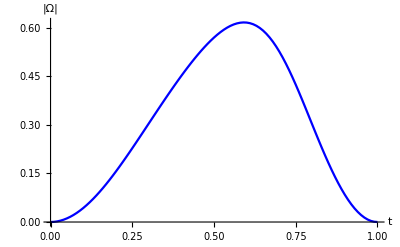

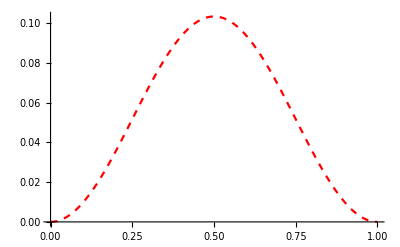

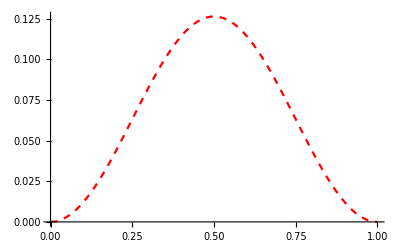

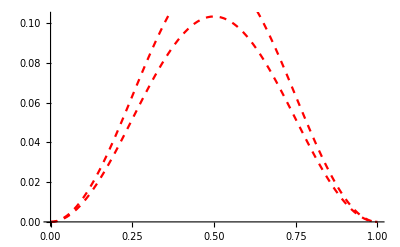

```mathematica
(*These are the coupling constants in GHz*)
g= 5; kx= 1; ki=  0.25; gam= 0.003; T=100;
d1=0; d2=0;
Cop=g^2/((ki+kx)*gam);
dp=0;eta=kx/(ki+kx)*(Cop/(1+Cop))-0.2;
bx1=DiscretePlot[{-Omega [xt*T, ki, kx, eta, T, dp, g, gam,  d1,d2]}, {xt, 0, 1, 0.01}, PlotRange->{Automatic, All}, PlotStyle->{{Blue}, {Black}, {Green}}, AxesLabel->{"t", "|Ω|"}]

(*bx1=DiscretePlot[{ Omega0[t , ki , kx , eta , T , dp , g , gam , d2 ]}, {xt, 0, 1.2, 0.001}, PlotRange->{Automatic, All}, PlotStyle->{{Blue}, {Black}, {Green}}, AxesLabel->{"t", "|Ω|"}]
*)(*bx2=DiscretePlot[{Sqrt[2*kx]Re[cgs[q*T, ki, kx, eta, T, dp, g, gam,d1, d2, {1, 0, 0}]], Re[Sqrt[eta]*coutperf[q*T, kx, T, dp]]}, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red},{Black, Dashed}}, AxesLabel->{"t", "cout"}]
 bx3=DiscretePlot[{Re[cus[q*T, ki, kx, eta, T, dp, g, gam,d1, d2, {1,0,0}]]}, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red},{Black, Dashed}}, AxesLabel->{"t", "cus"}, PlotRange->{All, {0, 1}}]*)
(*DiscretePlot[{Sqrt[2*kx]*Re[Exp[-I*Pi/4]cgs[q*T, ki, kx, eta, T, dp, g, gam,d1, d2, {1,0,0}]],Re[Sqrt[eta]*coutperf[q*T, kx, T, dp]]}, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red},{Black, Dashed}}, AxesLabel->{"t", "cgs"} ]*)
singleP=DiscretePlot[{ Re[ Sqrt[2*kx]cgs[q*T, ki, kx, eta-0.2, T, dp, g, gam,d1, d2, {1,0,0}]](*,Re[Sqrt[eta]*coutperf[q*T, kx, T, dp]]*)}, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red, Dashed}},PlotLegends->Placed[{" "," "," "}, { 0.74,0.7}] ]
singleP2=DiscretePlot[{ Re[ Sqrt[2*kx]cgs[q*T, ki, kx, eta, T, dp, g, gam,d1, d2, {1,0,0}]](*,Re[Sqrt[eta]*coutperf[q*T, kx, T, dp]]*)}, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red, Dashed}},PlotLegends->Placed[{" "," "," "}, { 0.74,0.7}] ]

Show[singleP, singleP2]
(* bx3=DiscretePlot[{Abs[cusc[q*T, ki, kx, Sin[Pi/10]^2, T, dp, g, gam,d1, d2, {Cos[Pi/3],0,0}, Pi/3]]^2}, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red},{Black, Dashed}}, AxesLabel->{"t", "cout"}, PlotRange->{All, {0, 1}}]*)
```

```mathematica
Sc[ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_,initx_, f_]:=Module[{soll, psic, w1c, w2c, w3c},
psic[t_]:={w1c[t],w2c[t],w3c[t]};
soll=NDSolve[LogicalExpand[ psic'[t]==-I*Hamc[t, ki, kx, eta, T, dp, g, gam, d1, d2].psic[t]+{0, 0, -Sqrt[2*kx]*f}&&psic[0]==initx],{w1c,w2c,w3c},{t,0,T}(*,AccuracyGoal->17,PrecisionGoal->15, WorkingPrecision->50*) (*(*Method->"DiscontinuityProcessing"->False,*)AccuracyGoal->17,PrecisionGoal->15, WorkingPrecision->50*)];
{w1c, w2c, w3c}/.soll
(*Plot[{Evaluate[psic[t]/. sol]^2, Sin[theeta]^2},{t,0,T}]*)]
Sr[ki_, kx_, eta_, T_, dp_, g_, gam_, d1_, d2_,initx_, f_]:=Module[{soll, psi, w1, w2, w3},
psi[t_]:={w1[t],w2[t],w3[t]};
soll=NDSolve[LogicalExpand[ psi'[t]==-I*Ham[t, ki, kx, eta, T, dp, g, gam, d1, d2].psi[t]+{0, 0, -Sqrt[2*kx]*f}&&psi[0]==initx],{w1,w2,w3},{t,0,T}(*,AccuracyGoal->17,PrecisionGoal->15, WorkingPrecision->50 *)(*(*Method->"DiscontinuityProcessing"->False,*)AccuracyGoal->17,PrecisionGoal->15,WorkingPrecision->50*)];
{w1, w2, w3}/.soll
(*Plot[{Evaluate[psic[t]/. sol]^2, Sin[theeta]^2},{t,0,T}]*)]
```

```mathematica
(*We now do the series of experiments*)
```

```mathematica
g= 5; kx= 1; ki= 0.25; gam=0.006/2; T= 100/kx;
d1=0; d2=0;
dp=0;


fopt[ki_ , kx_, gam_ , g_  ]:=Pi/8*Sqrt[ki/kx*g^2/(kx*gam)];

Ceiling[fopt[ki  , kx , gam  , g   ]]

ploss[ki_, kx_, gam_, g_, k_]:=ki/kx*(k+1)*Sin[Pi/(2*(2k+1))]^2+4*(k)*kx*gam/g^2;
ploss0[ki_, kx_, gam_, g_]:= 1-kx/(ki+kx)*(g^2/((ki+kx)*gam))/((g^2/((ki+kx)*gam))+1);
ploss0[ki , 0.5kx , gam , g ]
ploss[ki , 0.5kx , gam , g,34 ]
```

18

0.333393

0.0172279

i = 1

i = 2

i = 3

i = 4

i = 5

i = 6

i = 7

i = 8

i = 9

i = 10

i = 11

i = 12

i = 13

i = 14

i = 15

i = 16

i = 17

i = 18

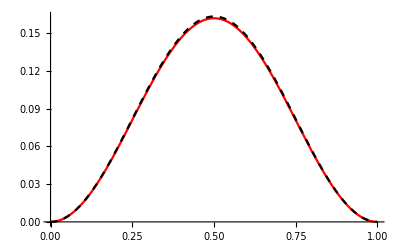

{3.33395×10^-8,0.0170919}

i = 19

```mathematica
tflip=1;
k=18 ;
theeta=Pi/(2*(2k+1));
eta= Sin[theeta]^2;
cs0=1;
fin=0;
thz= 0* Pi/3;
cgplotA={};
finA={};
foutA={};
eA={};
For[i=1, i<=k+1, i++,
(*F0=Sr[ki, kx, eta, T, dp, g, gam, d1 , d2 ,{-Exp[-I*Pi/2]cs0,0,0},fin];*)
(*If[i==1,F0=Sr[ki, kx, eta, T, dp, g, gam, d1 , d2 ,{-(*Exp[-I*thz]*)cs0,0,0},fin]; ];
If[i>1,F0=Sr[ki, kx, eta, T, dp, g, gam, d1 , d2 ,{-cs0,0,0},fin]; ];*)
F0=Sr[ki, kx, eta, T, dp, g, gam, d1 , d2 ,{cs0,0,0},fin];
F00[x_]=(F0[[1,3]])[x];
F02[x_]=(F0[[1,2]])[x];
F0s[x_]=(F0[[1,1]])[x];
Cout0[t_]=fin+Sqrt[2*kx]*F00[t];
Cs0[t_]=(F0[[1,1]])[t];
p0=NIntegrate[Abs[Cout0[x]]^2, {x, 0, T}];
s0=Abs[Cs0[T]]^2;
plota=DiscretePlot[{  Re[ Exp[-I*thz]*Cout0[q*T]],coutperf[q*T, kx, T, dp] }, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red },{Black, Dashed}, {Blue, Dotted}}];
plotb=DiscretePlot[{ Re[ F0s[q*T]]}, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red},{Black, Dashed}}, AxesLabel->{"t", "Retrievecs"}];
plotc=DiscretePlot[{ Re[ Exp[-I*thz]*F00[q*T]]}, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red, Dotted},{Black, Dashed}}, AxesLabel->{"t", "Retrievecg"}];
(*Print[plota];
Print[plotb];
Print[plotc];*)
(*Print["Cs0[T] = ",Cs0[T]];*)
(*Print[ plota];*)
(*Print[ (F0[[1,1]])[0]];*)
(*Print[plota];
Print[plotb];
Print[plotc];
Print[{s0, p0}];*)
(*Print[plotb];*)
AppendTo[cgplotA, F00[t]];
AppendTo[foutA, Cout0[t]];
AppendTo[finA, fin];
AppendTo[eA, F02[t]];
(*Print["AppendA"];*)
If[i==k+1, Print[ plota];Print[{s0, 1-p0}];];
Print["i = ", i];

(********************************************************************************)

F1=Sc[ki, kx, eta, T, dp, g, gam, d1 , d2 ,{    Cs0[T]   ,0,0}, Cout0[T-t]   ];
F11[x_]=(F1[[1,3]])[x];
F12[x_]=(F1[[1,2]])[x];
F1s[x_]=(F1[[1,1]])[x];
Cout1[t_]:=   Cout0[T-t]  +Sqrt[2*kx]*F11[t];
Cs1[t_]=(F1[[1,1]])[t];
p1=NIntegrate[Abs[Cout1[x]]^2, {x, 0, T}];
s1=Abs[Cs1[T]]^2;


plota=DiscretePlot[{  Re[  Exp[-I*thz]Cout1[q*T]],coutperf[q*T, kx, T, dp] }, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red, Dotted},{Black, Dashed}, {Blue, Dotted}}, AxesLabel->{"t", "Catch cout"}];
plotb=DiscretePlot[{  Abs[ Cs1[q*T]]}, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red},{Black, Dashed}}, AxesLabel->{"t", "Catchcs"}];
plotc=DiscretePlot[{ Re[ Exp[-I*thz]F00[q*T]]}, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Black, Dashed},{Black, Dashed}}, AxesLabel->{"t", "Catchcg"}];
(*Print[plotb];*)
(*Print[plota];
Print[ plotb ];
Print[ plotc ];
Print[{s1, p1}];*)
(*Print[ plotb ];
Print[plotc];
Print["Cs1[T] = ",Cs1[T]];*)
If[i!=(k+1),(*Print["AppendB"];*)
AppendTo[cgplotA,F11[t]];
AppendTo[finA, Cout0[T-t]];
AppendTo[foutA, Cout1[t]];
AppendTo[eA, F12[t]];
];




cs0= Cs1[T] ;
fin= Cout1[T-t] ;

(*fin=Cout1[t];*)
(*plotc=DiscretePlot[{  fin/.t->q}, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red},{Black, Dashed}}, AxesLabel->{"t", "plotc"}];
Print[plotc]*)
]
```

```mathematica
(k+1)*(ki/kx*Sin[Pi/(2*(2k+1))]^2+4*kx*gam/g^2)
(*a=Show[cgplot]*)
```

0.0348446

i = 1

i = 2

i = 3

i = 4

i = 5

i = 6

i = 7

i = 8

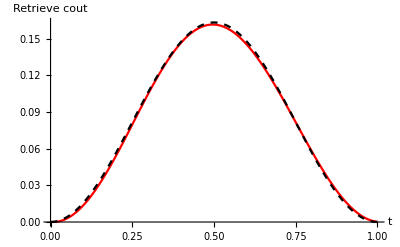

{0.0000292219,0.0219599}

i = 9

```mathematica
(*In this calculation, we don't flip*)
tflip=0;
k=8;
theeta=Pi/(2*(2k+1));
eta= Sin[theeta]^2;
cs0=1;
fin=0;
(*thz=Pi/3;*)
cgplotB={};
finB={};
foutB={};
eB={};
For[i=1, i<=k+1, i++,
(*F0=Sr[ki, kx, eta, T, dp, g, gam, d1 , d2 ,{-Exp[-I*Pi/2]cs0,0,0},fin];*)
(*If[i==1,F0=Sr[ki, kx, eta, T, dp, g, gam, d1 , d2 ,{-(*Exp[-I*thz]*)cs0,0,0},fin]; ];
If[i>1,F0=Sr[ki, kx, eta, T, dp, g, gam, d1 , d2 ,{-cs0,0,0},fin]; ];*)
F0=Sr[ki, kx, eta, T, dp, g, gam, d1 , d2 ,{cs0,0,0},fin];
F00[x_]=(F0[[1,3]])[x];
F02[x_]=(F0[[1,2]])[x];
F0s[x_]=(F0[[1,1]])[x];
Cout0[t_]=fin+Sqrt[2*kx]*F00[t];
Cs0[t_]=(F0[[1,1]])[t];
p0=NIntegrate[Abs[Cout0[x]]^2, {x, 0, T}];
s0=Abs[Cs0[T]]^2;
plota=DiscretePlot[{  Re[ Exp[-I*thz]Cout0[q*T]],coutperf[q*T, kx, T, dp] }, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red },{Black, Dashed}, {Blue, Dotted}}, AxesLabel->{"t", "Retrieve cout"}];
plotb=DiscretePlot[{ Re[Exp[-I*thz]F0s[q*T]]}, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red},{Black, Dashed}}, AxesLabel->{"t", "Retrievecs"}];
plotc=DiscretePlot[{ Re[ Exp[-I*thz]F00[q*T]]}, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Magenta, Dotted},{Black, Dashed}}, AxesLabel->{"t", "Retrievecg"}];
(*Print[ (F0[[1,1]])[0]];*)
AppendTo[cgplotB, F00[t]];
AppendTo[foutB, Cout0[t]];
AppendTo[finB, fin];
AppendTo[eB,F02[t]];
(*Print[ plota];*)
(*Print["AppendA"];*)
If[i==k+1, Print[ plota];Print[{s0,1- p0}];
];

(********************************************************************************)
F1=Sc[ki, kx, eta, T, dp, g, gam, d1 , d2 ,{    Cs0[T]   ,0,0},   Cout0[t]   ];
F11[x_]=(F1[[1,3]])[x];
F12[x_]=(F1[[1,2]])[x];
F1s[x_]=(F1[[1,1]])[x];
Cout1[t_]=   Cout0[t]  +Sqrt[2*kx]*F11[t];
Cs1[t_]=(F1[[1,1]])[t];
p1=NIntegrate[Abs[Cout1[x]]^2, {x, 0, T}];
s1=Abs[Cs1[T]]^2;


plota=DiscretePlot[{  Re[  Exp[-I*thz]Cout1[q*T]],coutperf[q*T, kx, T, dp] }, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red, Dotted},{Black, Dashed}, {Blue, Dotted}}, AxesLabel->{"t", "Catch cout"}];
plotb=DiscretePlot[{  Abs[Cs1[q*T]]}, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red},{Black, Dashed}}, AxesLabel->{"t", "Catchcs"}];
plotc=DiscretePlot[{ Re[ Exp[-I*thz]F00[q*T]]}, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Blue, Dashed},{Black, Dashed}}, AxesLabel->{"t", "Catchcg"}];
(*Print[plota];
Print[ plotb ];
Print[ plotc ];
Print[{s1, p1}];*)
If[i!=(k+1),(*Print["AppendB"];*)
AppendTo[cgplotB, F11[t]];
AppendTo[finB, Cout0[t]];
AppendTo[foutB, Cout1[t]];
AppendTo[eB,F12[t]];
];



cs0= Cs1[T] ;
 fin= Cout1[t] ; 
 

(*fin=Cout1[t];*)
(*plotc=DiscretePlot[{  fin/.t->q}, {q, 0, 1,0.01}, AxesOrigin->{0, 0}, PlotStyle->{{Red},{Black, Dashed}}, AxesLabel->{"t", "plotc"}];
Print[plotc]*)
Print["i = ", i];
]
```

```mathematica
(k+1)*(ki/kx*Sin[Pi/(2*(2k+1))]^2+4*kx*gam/g^2)
```

0.009531

```mathematica
eta//N
```

0.25

```mathematica
finAA[x_]:= finA/.t->x;
finBB[x_]:= finB/.t->x;
foutAA[x_]:= foutA/.t->x;
foutBB[x_]:= foutB/.t->x;
cgAA[x_]:=Exp[-I*thz]*cgplotA/.t->x;
cgBB[x_]:=Exp[-I*thz]*cgplotB/.t->x;
eAA[x_]:=eA/.t->x;
eBB[x_]:=eB/.t->x;
coutApproxG[t_, f_,  initS_]:=f +  Sin[theeta]*Sqrt[2*kx]*Exp[I*Pi/3]*1/Sqrt[2*kx]*h[t, T]*initS;
coutApprox1[t_]:=coutApproxG[t ,0,  1];
coutApprox2[t_]:=coutApproxG[t ,coutApprox1[t],  Cos[2*theeta]];
coutApprox3[t_]:=coutApproxG[t ,coutApprox2[t],  Cos[3*theeta]];
coutApprox4[t_]:=coutApproxG[t ,coutApprox3[t],  Cos[4*theeta]];
coutApprox5[t_]:=coutApproxG[t ,coutApprox4[t],  Cos[5*theeta]];
coutApprox6[t_]:=coutApproxG[t ,coutApprox5[t],  Cos[6*theeta]];
coutApprox7[t_]:=coutApproxG[t ,coutApprox6[t],  Cos[7*theeta]];
```

```mathematica
DiscretePlot[{ Re[foutBB[x*T]][[1]] }, {x, 0,1, 0.01}, PlotStyle->{{Red, Dashed}, {Green, DotDashed}, {Magenta, Dotted}}]
```

$Aborted

```mathematica
DiscretePlot[{ Re[foutAA[x*T]][[20;;34]] }, {x, 0,1, 0.01}, PlotStyle->{{Red, Dashed}, {Green, DotDashed}, {Magenta, Dotted}}]
(*DiscretePlot[{ Re[cgAA[x*T]][[1;;6]] }, {x, 0,1, 0.01}, PlotStyle->{{Red, Dashed}, {Green, DotDashed}, {Magenta, Dotted}}]*)
(*DiscretePlot[{Re[coutApprox2[x*T]], Re[foutAA[x*T]][[2]],Re[Exp[I*thz]*h[x*T, T]*Sin[theeta]]*(1+Cos[2*theeta])}, {x, 0,1, 0.01}, PlotStyle->{{Red, Dashed}, {Green, DotDashed},  {Magenta, Dotted}}]
DiscretePlot[{Re[coutApprox3[x*T]], Re[foutAA[x*T]][[3]], Re[Exp[I*thz]*h[x*T, T]*Sin[theeta]]*(1+Cos[2*theeta]+Cos[3*theeta])}, {x, 0,1, 0.01}, PlotStyle->{{Red, Dashed}, {Green, DotDashed}, {Magenta, Dotted}}]
DiscretePlot[{Re[coutApprox7[x*T]], Re[foutAA[x*T]][[7]], Re[Exp[I*thz]*h[x*T, T]*Sin[theeta]]*(1+Cos[2*theeta]+Cos[3*theeta]+Cos[4*theeta]+Cos[5*theeta]+Cos[6*theeta]+Cos[7*theeta])}, {x, 0,1, 0.01}, PlotStyle->{{Red, Dashed}, {Green, DotDashed}, {Magenta, Dotted}}]*)
```

$Aborted

$Aborted

```mathematica
fp1=DiscretePlot[{Re[Exp[-I*thz]*foutAA[x]],Sin[5*theeta]*coutperf[x, kx, T, 0], Sin[theeta]*coutperf[x, kx, T, 0]}, {x, T, 0, -1}, PlotStyle->{{Red, Dashed}, {Green, "*-"}, Green}];
(*fp2=DiscretePlot[Re[Exp[-I*thz]*foutAA[T-x]], {x, 0, T, 1}, PlotStyle->{ {Blue, DotDashed}, Green}];
Show[fp1, fp2]
fp1=DiscretePlot[Re[Exp[-I*thz]*foutBB[x]], {x, T, 0, -1}, PlotStyle->{{Red, Dashed}, {Blue}, Green}];
fp2=DiscretePlot[Re[Exp[-I*thz]*foutBB[T-x]], {x, 0, T, 1}, PlotStyle->{ {Blue, DotDashed}, Green}];
Show[fp1, fp2]*)
```

$Aborted

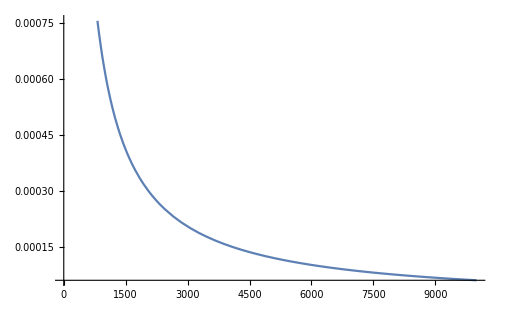

```mathematica
f[k_]:=Sum[Sin[j*Pi/(2*(2k+1))]^2, {j, 1, 2k+1}];
f2[k_]:=Sin[Pi/(2*(2k+1))]^2 Sum[Cos[j*Pi/(2*(2k+1))]^2, {j, 0, 2k}];
f3[k_]:=Sin[Pi/(2*(2k+1))]^2*Sum[Cos[Pi/(2*(2k+1))*j]^2, {j, 0, 2k}]
Plot[f2[k], {k, 1, 10000}]
```

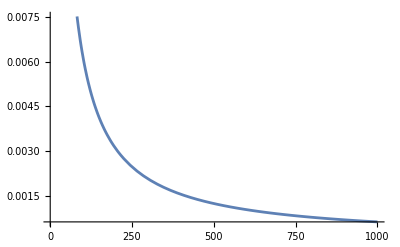

```mathematica
Plot[SumA[a], {a, 1, 1000}]
```

```mathematica
ki=0.1; kx=1; g=6; gam=0.0061/2;
g/gam
Cop=g^2/(kx*gam);
ki/kx+Cop^-1;
1-kx/(ki+kx)*(Cop/(1+Cop))
pl[k_]:=ki/kx*Sin[Pi/(2(2k+1))]^2*(k+1)+4*(k+1)*kx*gam/g^2;

DiscretePlot[{pl[n], 0.1, pl[12]}, {n, 1, 50, 1}];
pl[12]
```

1967.21

0.0909861

0.009531

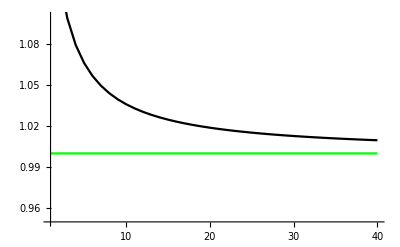

```mathematica
DiscretePlot[{f[k, Pi/(2*(2*k+1))], Sqrt[2]*Cos[Pi/(4*(2*k+1))]*Cos[k*Pi/(2*(2*k+1))],1}, {k, 1,40}, PlotRange->{All, {  0.95, 1.1}}, PlotStyle->{Red, Black, Green}]
(*DiscretePlot[{f[k, Pi/(2*(2*k+1))], Sqrt[2]*Cos[Pi/(4*(2*k+1))]*Cos[k*Pi/(2*(2*k+1))],1}, {k, 1,16}, PlotRange->{All, {  0.95, 1}}, PlotStyle->{Red, Black, Green}]
DiscretePlot[{Sqrt[2]*Cos[Pi/(4*(2*k+1))]*Cos[k*Pi/(2*(2*k+1))],f[k, Pi/(2*(2*k+1))]}, {k, 1,160}, PlotRange->{All, { 0,1.1}}, PlotStyle->{Red, Black}]*)
```

```mathematica
f[n_]:=Exp[-n/2] n^(n/2)/Sqrt[n!];

g[n_, δ_]:=Log[2/δ]/f[n]-1;
g2[n_, δ_]:=(2*Pi)^(1/4)(Log[2/δ])*n^(1/4)-1;
g3[n_, δ_]:=1.6(Log[2/δ]-1)*n^(1/4)-1;
```

SetDelayed::write: Tag Integer in 5[n_,δ_] is Protected.

```mathematica
(*Plot[{g[n, Sqrt[1-(2*0.99999-1)^2]], 4*1.58*Sqrt[n](*,g2[n, 0.0001], g3[n, 0.0001]*)}, {n, 1,20}, PlotStyle->{Red, Green}];*)
pf1=Plot[{g[n, Sqrt[1-(0.999)]], 4*1.04*Sqrt[n](*,g2[n, 0.0001], g3[n, 0.0001]*)}, {n, 1,30}, PlotStyle->{Red, {Red, Dashed}}, PlotRange->{All, {0, 35}}];
pf2=Plot[{g[n, Sqrt[1-(0.9999)]], 4*1.28*Sqrt[n](*,g2[n, 0.0001], g3[n, 0.0001]*)}, {n, 1,30}, PlotStyle->{Green, {Green, Dashed}}, PlotRange->{All, {0, 35}}];
pf3=Plot[{g[n, Sqrt[1-(0.99999)]], 4*1.58*Sqrt[n](*,g2[n, 0.0001], g3[n, 0.0001]*)}, {n, 1,30}, PlotStyle->{Blue, {Blue, Dashed}}, PlotRange->{All,  {0, 35}}];
plotFock =Show[{pf3, pf1}, PlotRange->{All,{0, 35}}];
(*Export["SNAP.eps",plotFock]*)
```

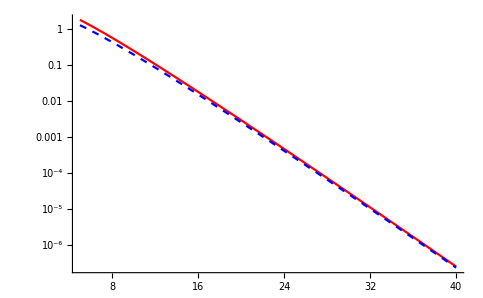

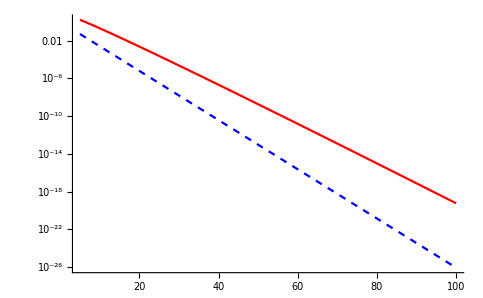

```mathematica
(*Noon state analysis*)
ErrNoon[n_, δ_]:=(Log[2/δ]/f[n]-1)Exp[-n/2];
ep[ l_, n_]:=2*l*Exp[-n/2];
f[n_]:=Exp[-n/2] n^(n/2)/Sqrt[n!];
del[l_, n_]:=2Exp[-2*l*f[n]];
ErrFidNoon[n_, δ_]:=1-Sqrt[1-δ^2]*(1-ErrNoon[n, δ]);
ErrFidNoon2[n_, l_]:=1-Sqrt[1-4Exp[-10*l/(4*n^(1/4))]]*(1-2l*Exp[-n/2])
ErrFidNoon3[n_, l_]:=1-(1-2*del[l, n]^2)*(1-ep[n, l])(1-Exp[-n]/2);
ErrorFidNoon4[n_, l_]:=2*(del[l, n]^2(*+ep[l, n]*)+Sqrt[2*ep[l, n]]*del[l, n]-ep[l, n]*del[l, n]^2+Exp[-n]/2);
ErrorFidNoon5[n_, l_]:=2*(del[l, n]^2+ep[l, n]+Sqrt[2*ep[l, n]]*del[l, n]-ep[l, n]*del[l, n]^2+Exp[-n]/2);
y[n_, l_]:=2*(del[l, n]^2+ Sqrt[2*ep[l, n]]*del[l, n] );


(*Plot[ErrFidNoon[n, Sqrt[1-(0.999999)]], {n, 1, 26}, ScalingFunctions->{None, "Log"}]
(*p1=Plot[{ErrFidNoon2[n,n^(5/4)/5],ErrFidNoon2[n,2 n^(2/4)]}, {n, 5,50}, ScalingFunctions->{None, "Log"}, PlotStyle->{{Red, Dashed}, {Black, Dashed}}]*)
p1=Plot[{ErrFidNoon3[n,0.2*n^(5/4)+0.92*n^(1/4)],ErrFidNoon3[n,0.2*n^(5/4) ]}, {n, 5,26}, ScalingFunctions->{None, "Log"}, PlotStyle->{{Red, Dashed}, {Green, Dashed}}]*)

a=(2*Pi)^(1/4)/2;
p1=Plot[{ErrorFidNoon4[n,a/4*n^(5/4) ],ErrorFidNoon4[n, 3*n^(1/2)] ,ErrorFidNoon4[n, 2*n^(1/2)]}, {n, 5,55}, ScalingFunctions->{None, "Log"}, PlotStyle->{{Red }, {Blue, Dashed}, {Green, Dashed}}, PlotLegends->Placed[{" "," "," "}, { 0.8,0.7}]];
p1=Plot[{(*ErrorFidNoon4[n,a/4*n^(5/4) ],*)ErrorFidNoon5[n,a/4*n^(5/4) ], n^(5/8)Exp[-n/2]*(4Sqrt[a]+n^(5/8)a)}, {n, 5,40}, ScalingFunctions->{None, "Log"}, PlotStyle->{{Red }, {Blue, Dashed}, {Green, Dashed}}, PlotLegends->Placed[{" "," "," "}, { 0.8,0.7}]]
p1=Plot[{ ErrorFidNoon5[n,(a*0.6)/2*n^(5/4) ],   Exp[-0.6*n] }, {n, 5,100}, ScalingFunctions->{None, "Log"}, PlotStyle->{{Red }, {Blue, Dashed}, {Green, Dashed}}, PlotLegends->Placed[{" "," "," "}, { 0.8,0.7}]]
 
(*Plot[{y[n,a/4*n^(5/4) ],4*( Exp[-n/2]*( Sqrt[a ]*n^(5/8))  +Exp[-n/2] ) (* 2^(13/8)Pi^(1/8)*n^(5/8)Exp[-n/2]*)}, {n, 5,50}, ScalingFunctions->{None, "Log"}, PlotStyle->{{Red }, {Blue, Dashed}, {Green, Dashed}}, PlotLegends->Placed[{" "," "," "}, { 0.8,0.7}]]
 *)

(*Export["NoonErr.eps",p1]*)
(*Plot[g[n, Sqrt[1-(0.999999)]], {n, 1, 26} ]*)
```

8333.33

6.80175

0.0180607

0.0912423

1000.

2.26725

444.444

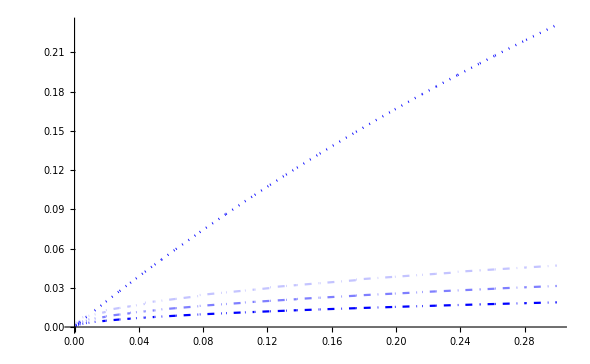

```mathematica
ploss[ki_, kx_, gam_, g_, k_]:=ki/kx*(k+1)*Sin[Pi/(2*(2k+1))]^2+4*k*kx*gam/g^2;
ploss0[ki_, kx_, gam_, g_]:= 1-kx/(ki+kx)*(g^2/((ki+kx)*gam))/((g^2/((ki+kx)*gam))+1);

plossapprx[ki_, kx_, gam_, g_, k_]:= 4*(k)*kx*gam/g^2+Pi^2/(16*k)*ki/kx;
Cex[ki_, kx_, gam_, g_ ]:=(kx*gam/g^2)^-1;
f11[k_]:=(k+1)*Sin[Pi/(2*(2k+1))]^2;
fopt[ki_, kx_, gam_, g_ ]:=Pi/8*Sqrt[ki/kx*g^2/(kx*gam)];

plossOpt[ki_ , kx_ , gam_, g_  ]:=ploss[ki , kx , gam , g , Ceiling[fopt[ki  , kx , gam , g  ]]];


Cex[0.1, 1, 0.003, 5]
fopt[0.1, 1, 0.003, 3]
ploss[0.1, 1, 0.003, 3, fopt[0.1, 1, 0.003, 3]]
ploss0[0.1, 1, 0.003, 3]
Cex[0.1, 3, 0.003, 3]
fopt[0.1, 3, 0.003, 3]
Cex[0.1, 3, 0.003, 2]
Plot[{ploss[0.1, 1, 0.003, 3, k], ploss0[0.1,1, 0.003, 3, k], ploss[0.1, 3, 0.003, 3, k], ploss0[0.1,3, 0.003, 3, k]}, {k, 1, 15}, PlotStyle->{{Red},{Red, Dashed}, {Green},{Green, Dashed}}];
Plot[{ploss[0.1, 1, 0.003, 3, k], plossapprx[0.1,1, 0.003, 3, k]}, {k, 1, 15}, PlotStyle->{{Red, Dashed},{Green, Dashed}}];
(*Plot[{f11[n], Pi^2/(16n)},{n, 1, 12}, PlotStyle->{Red, {Green, Dashed}}]*)
lossplot =Plot[{ plossOpt[x, 1, 0.003, 5], plossOpt[x, 1, 0.003, 3],plossOpt[x, 1, 0.003,2], ploss0[x,1, 0.003, 5],ploss0[x,1, 0.003, 3],ploss0[x,1, 0.003, 2]}, {x, 0, 0.3}, PlotStyle->{{Directive[Blue,Opacity[1]],DotDashed},{Directive[Blue,Opacity[0.5]],DotDashed},{Directive[Blue,Opacity[0.23]],DotDashed},{Directive[Blue,Opacity[1]], Dotted},{Directive[Blue,Opacity[0.4]], Dotted},{Directive[Blue,Opacity[0.15]], Dotted}} ,PlotLegends->Placed[{" "," "," "}, { 0.80,0.55}]]
(* Plot[{Ceiling[fopt[x, 1, 0.003, 5]], Ceiling[fopt[x,1, 0.003, 3]], Ceiling[fopt[x, 1, 0.003, 2]], Ceiling[fopt[x,1, 0.003, 2]], Ceiling[fopt[x, 1, 0.003, 1]], Ceiling[fopt[x,1, 0.003, 1]]}, {x, 0, 0.3}, PlotStyle->{{Red},{Red, Dashed}, {Green},{Green, Dashed}}]*)

(*Export["lossplot2.eps",lossplot]*)
```

```mathematica
plossOpt[0.1, 1, 0.003, 6]
 ploss0[0.1,1, 0.003, 6]
```

0.00939653

0.0909924

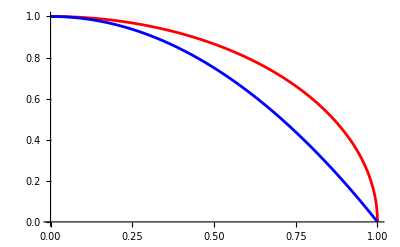

```mathematica
Plot[{ Sqrt[1-x^2], 1-x^2}, {x,  0, 1}, PlotStyle->{Red, Blue }]
```

```mathematica
(1-ϵ)(1-δ^2)-δ^2(1-ϵ)//Simplify
```

(-1+2 δ^2) (-1+ϵ)

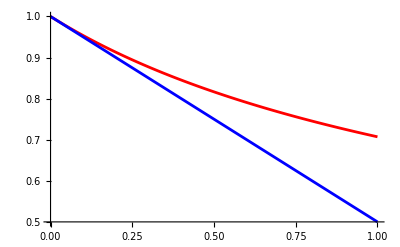

```mathematica
Plot[{ 1/Sqrt[1+x], 1-x/2}, {x,  0, 1}, PlotStyle->{Red, Blue}]
```

```mathematica
(1-2 δ^2)(1-ϵ)(1-Exp[-n])//Simplify
```

ⅇ^-n (-1+ⅇ^n) (-1+2 δ^2) (-1+ϵ)

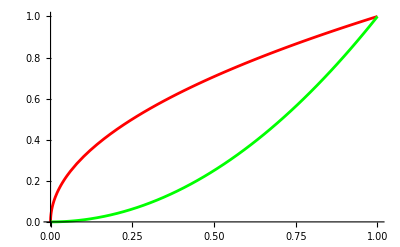

```mathematica
Plot[{Sqrt[x], x^2}, {x, 0, 1}, PlotStyle->{Red, Green}]
```

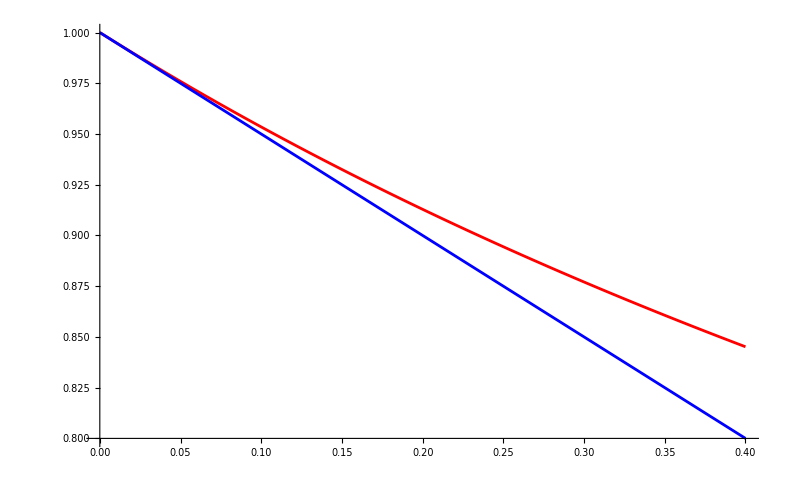

```mathematica
Plot[{1/Sqrt[1+x], 1-x/2}, {x,  0, 0.4}, PlotStyle->{Red, Blue }]
```

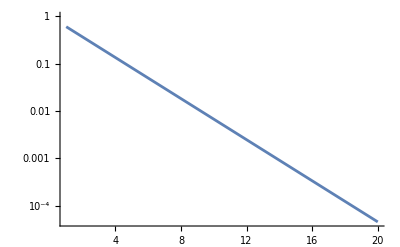

```mathematica
Plot[Exp[-n/2], {n, 1, 20}, ScalingFunctions->{None, "Log"}]
```

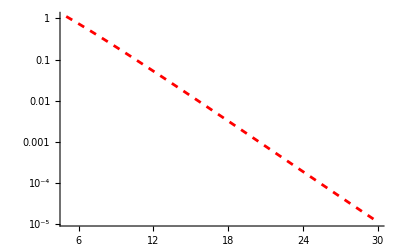

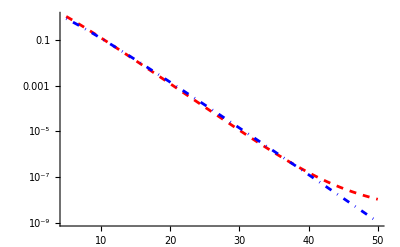

```mathematica
f[a_, l_, n_]:=4Exp[-2*l/(a*n^(1/4))]*(1-2*l*Exp[-n/2])+2*l*Exp[-n/2]+4*Exp[-n/4]*Exp[-l/(a*n^(1/4))]*Sqrt[l];
Plot[{f[(2*Pi)^(1/4)/2, n^(5/4)*(2*Pi)^(1/4)/(2*4), n],f[(2*Pi)^(1/4)/2,(a/2+5) n^(1/4), n]}, {n,5, 300}, ScalingFunctions->{None, "Log"}, PlotStyle->{Red, Blue}];
Plot[{f[(2*Pi)^(1/4)/2,(5)( a*n^(1/4)/2), n],f[(2*Pi)^(1/4)/2,(5)( a*n^(2/4)/2), n],4 Exp[-5]}, {n,5, 30}, ScalingFunctions->{None, "Log"}, PlotStyle->{{Red, Dashed}, {Blue, DotDashed}}];
Plot[{f[(2*Pi)^(1/4)/2, ( 3*n^0.5), n] }, {n,5, 30}, ScalingFunctions->{None, "Log"}, PlotStyle->{{Red, Dashed}, {Blue, DotDashed}}]

Plot[{f[(2*Pi)^(1/4)/2, ( 3*n^0.5), n] , f[(2*Pi)^(1/4)/2, ( a*n^(5/4))/4, n] }, {n,5, 50}, ScalingFunctions->{None, "Log"}, PlotStyle->{{Red, Dashed}, {Blue, DotDashed}}]
```

```mathematica
(2*Pi)^(1/4)/(2*4)//N
```

0.197904

```mathematica
a/2//N
```

0.631619

```mathematica
a
```

π^(1/4)/2^(3/4)

```mathematica
(2*Pi)^(1/4)/2//N
```

0.791617

photon.eps

Sin[3 x]

```mathematica
TrigReduce[Sin[x]-2 Sin[x]^3-2Sin[x] Cos[x]^2]
```

```mathematica
TrigReduce[(-Sin[x]+2 Sin[x]^3)]
```

1/2 (Sin[x]-Sin[3 x])

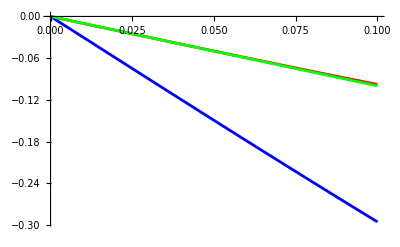

```mathematica
f[x_]:=-Sin[x]+2 Sin[x]^3;
f2[x_]:=Sin[3x];

Plot[{f[x], -Sin[3x], -Sin[x]}, {x, 0, 0.1}, PlotStyle->{Red, Blue, Green}]
```

```mathematica
Series[Sin[x](1-4 Cos[x]^2), {x, 0, 3}]
Series[Sin[x](1-2 Cos[x]^2), {x, 0, 3}]
Series[Sin[x](1-3 Cos[x]^2), {x, 0, 3}]
```

-3 x+(9 x^3)/2+O[x]^4

-x+(13 x^3)/6+O[x]^4

-2 x+(10 x^3)/3+O[x]^4

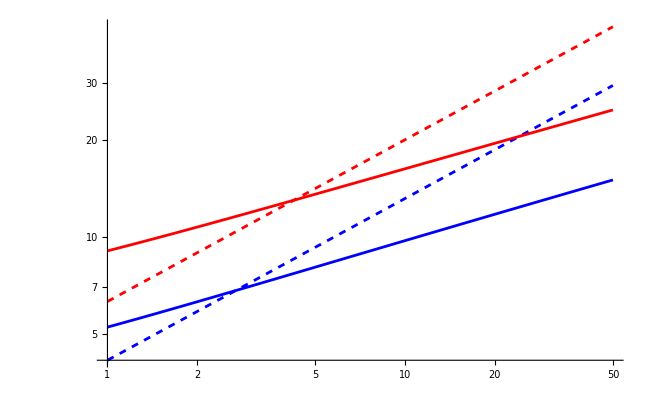

0.0447102

0.00447212

0.99998

0.998001

```mathematica
f[n_]:=Exp[-n/2] n^(n/2)/Sqrt[n!];
gc[n_,δ_]:=(Log[2/δ]/f[n]-1);
p2=Plot[{    }, {n, 1, 50}, PlotStyle->{{Red, Dashed}, {Blue, Dashed}}, PlotRange->{All, All}, ScalingFunctions->{"Log", "Log"} ,PlotLegends->Placed[LineLegend[{" "," "},LegendMarkerSize->30,LegendMargins->0.01],{0.15,0.7}]];
p3=Plot[{gc[n, Sqrt[1-0.999^2]], 4*1.04*Sqrt[n] , gc[n, Sqrt[1-0.99999^2]], 4*1.58*Sqrt[n] }, {n, 1, 50}, PlotStyle->{Blue, {Blue, Dashed}, Red, {Red, Dashed} }, PlotRange->{All, All}, ScalingFunctions->{"Log", "Log"} ,PlotLegends->Placed[LineLegend[{" "," ", " ", " "},LegendMarkerSize->40,LegendMargins->0.4],{0.2,0.4}]];
(*p2=Plot[{  gc[n, Sqrt[1-0.99999^2]], 4*1.58*Sqrt[n] }, {n, 1, 50}, PlotStyle->{{Red, Dashed}, {Blue, Dashed}}, PlotRange->{All, All}, ScalingFunctions->{"Log", "Log"} ,PlotLegends->Placed[LineLegend[{" "," "},LegendMarkerSize->30,LegendMargins->0.01],{0.15,0.7}]];*)

Show[  p3]
Sqrt[1-0.999^2]
Sqrt[1-0.99999^2]

 0.99999^2
 0.999^2
(*p2=Plot[{gc[n, Sqrt[1-0.99999]],gc[n, Sqrt[1-0.99999^2]], 4*1.58*Sqrt[n] }, {n, 1, 50}, PlotStyle->{Blue, White, {Blue, Dashed}}, PlotRange->{{1, All}, {1, All}}, ScalingFunctions->{"Log", "Log"}, PlotLegends->Placed[{" "," "," "}, { 0.74,0.4}]];*)
(*hmm=Show[p2, p1]*)

(*Export["SNAPcount.eps",p3]*)
```

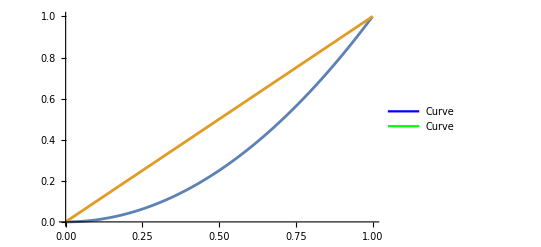

```mathematica
Plot[{x^2, x},{x,0,1},Epilog->Inset[LineLegend[ {Blue, Green},{"Curve", "Curve"} ],Scaled[{0.4,0.8}]]]
```

```mathematica
Sqrt[1-0.99999]
Sqrt[1-0.99999^2]
```

0.00316228

0.00447212

```mathematica
ploss[ki_, kx_, gam_, g_, k_]:=ki/kx*(k+1)*Sin[Pi/(2*(2k+1))]^2+4*(k)*kx*gam/g^2;
ploss0[ki_, kx_, gam_, g_]:= 1-kx/(ki+kx)*(g^2/((ki+kx)*gam))/((g^2/((ki+kx)*gam))+1);

plossapprx[ki_, kx_, gam_, g_, k_]:= 4*(k+1)*kx*gam/g^2+Pi^2/(16*k)*ki/kx;
Cex[ki_, kx_, gam_, g_ ]:=(kx*gam/g^2)^-1;
f11[k_]:=(k+1)*Sin[Pi/(2*(2k+1))]^2;
fopt[ki_, kx_, gam_, g_ ]:=Pi/8*Sqrt[ki/kx*g^2/(kx*gam)];

plossOpt[ki_ , kx_ , gam_, g_  ]:=ploss[ki , kx , gam , g , Ceiling[fopt[ki  , kx , gam , g  ]]];


(*Cex[0.1, 1, 0.003, 5]
fopt[0.1, 1, 0.003, 3]
ploss[0.1, 1, 0.003, 3, fopt[0.1, 1, 0.003, 3]]
ploss0[0.1, 1, 0.003, 3]
Cex[0.1, 3, 0.003, 3]
fopt[0.1, 3, 0.003, 3]
Cex[0.1, 3, 0.003, 2]*)
ki=0.2; 
kx=1; 
g=7;
gam=0.000000003;
ploss0[ki , kx , gam , g ]
ki/(ki+kx)
plossapprx[ki , kx , gam , g ,Ceiling[fopt[ki , kx , gam , g ]] ]
Pi*Sqrt[ki/kx*kx*gam/g^2]
```

0.166667

0.166667

0.0000109935

0.0000109933

```mathematica
140.2948-103.5821
```

36.7127

```mathematica
60.5376-36.71270000000001
```

23.8249

```mathematica
(*Plotting stuff*)
SetDirectory[NotebookDirectory[]]
files=FileNames["ACsPop*.csv"];
files1=FileNames["BPop*.csv"];
files2=FileNames["m*.csv"];
Directory[]
```

/Users/sharoonaustin/Library/CloudStorage/OneDrive-Personal/Documents/FockStatePaper/Code

/Users/sharoonaustin/Library/CloudStorage/OneDrive-Personal/Documents/FockStatePaper/Code

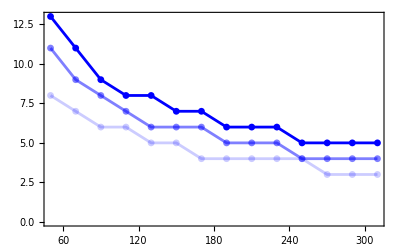

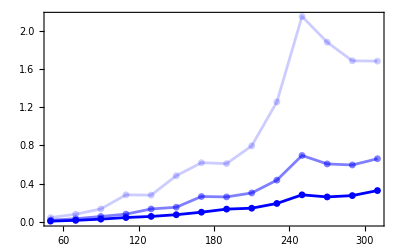

kmin.eps

Loss.eps

```mathematica
dataA=Table[Flatten@Import["ACsPop"<>ToString[i]<>".csv"],{i,1, 14,1}];
indicesA=First/@(Ordering[#,1]&/@dataA);
datam=Table[Flatten@Import["m"<>ToString[i]<>".csv"],{i,1, 14,1}];
indicesm=First/@(Ordering[#,1]&/@datam);
dataB=Table[Flatten@Import["BPop"<>ToString[i]<>".csv"],{i,1, 14,1}];
indicesB=First/@(Ordering[#,1]&/@dataB);

plotAt=Table[{(0.5+(i-1)*0.2)*100,indicesA[[i]] }, {i, 1, 14, 1}];
plotmt=Table[{(0.5+(i-1)*0.2)*100,indicesm[[i]] }, {i, 1, 14, 1}];
plotBt=Table[{(0.5+(i-1)*0.2)*100,indicesB[[i]] }, {i, 1, 14, 1}];
plotAlt=Table[{(0.5+(i-1)*0.2)*100,dataA[[i,indicesA[[i]] ]]*10^8}, {i, 1, 14, 1}];
plotmlt=Table[{(0.5+(i-1)*0.2)*100,datam[[i,indicesm[[i]] ]]*10^8}, {i, 1, 14, 1}];
plotBlt=Table[{(0.5+(i-1)*0.2)*100,dataB[[i,indicesB[[i]] ]]*10^8}, {i, 1, 14, 1}];

common={PlotRange->{{0.5*100,3.1*100},All},PlotStyle->{{Directive[Blue,Opacity[0.2]] },{Directive[Blue,Opacity[0.5]] },{Directive[Blue,Opacity[1]] }},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->400,ImagePadding->{{65,20},{45,20}},Axes->True,TicksStyle->Black,LabelStyle->Black};
(*
kmin=ListLinePlot[{plotAt,plotmt,plotBt},Evaluate@common,PlotLegends->Placed[LineLegend[{" "," ", " "},LegendMarkerSize->40,Spacings->0.05],{0.7,0.8}]];*)
kmin=ListLinePlot[{plotAt,plotmt,plotBt},Evaluate@common,PlotLegends->Placed[LineLegend[{" "," "," "},Spacings->0.5,LegendMarkers->None],{0.7,0.7}], Frame->True,PlotMarkers->{"●",7}]
Loss=ListLinePlot[{plotAlt,plotmlt,plotBlt},Evaluate@common,PlotLegends->Placed[LineLegend[{" "," ", " "},Spacings->0.5 ,LegendMarkers->None],{0.2,0.7}], ScalingFunctions->{None, None}, Frame->True,PlotMarkers->{"●",7}]

Export["kmin.eps",kmin]
Export["Loss.eps",Loss]
```

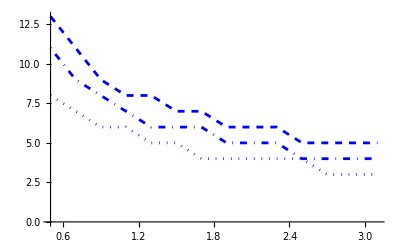

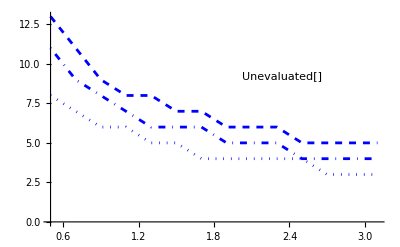

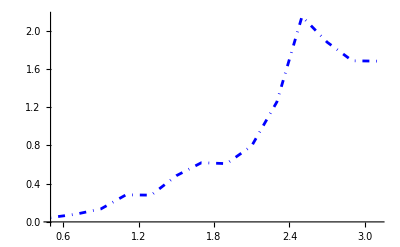

```mathematica
Loss=ListLinePlot[{(*plotAlt,*)plotAlt},Evaluate@common,PlotLegends->Placed[LineLegend[{" "," "},LegendMarkerSize->40,Spacings->0.05],{0.2,0.8}]]
```

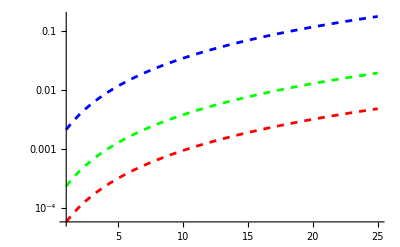

-Graphics-

p1.eps

```mathematica
llpl=ListLinePlot[{ Flatten[dataocc0^2],Flatten[dataocc1^2], Flatten[dataocc2^2]},PlotRange->{{1,24},All} ,ScalingFunctions->{None, "Log"}, PlotStyle->{Red, Green, Blue} , PlotLegends->Placed[{" "," "," "}, { 0.8,1}]];
llpl22=ListLinePlot[{ Flatten[dataocc0^2],Flatten[dataocc1^2], Flatten[dataocc2^2]},PlotRange->{{1,24},All} ,ScalingFunctions->{"Log", "Log"}, PlotStyle->{Red, Green, Blue} ];

err[g_, kx_, T_, k_]:= kx/(g^2*T)*Sqrt[4*Pi^2/3]*(10.2+5.1k);
 errana=Plot[{err[6,0.5, 100, k]^2,err[6, 1, 100, k]^2,err[6, 3, 100, k]^2 }, {k, 1, 25}, ScalingFunctions->{None, "Log"}, PlotStyle->{{Red, Dashed},{Green, Dashed},{Blue, Dashed}} ]
 errana2=Plot[{err[6,0.5, 100, k]^2,err[6, 1, 100, k]^2,err[6, 3, 100, k]^2}, {k, 1, 25}, ScalingFunctions->{"Log", "Log"}, PlotStyle->{{Red, Dashed},{Green, Dashed},{Blue, Dashed}}];
broo=Show[ errana,llpl, PlotRange->{All, All} ]
(*Show[ errana2,llpl22, PlotRange->{All, All}];*)

Export["p1.eps",broo]
```

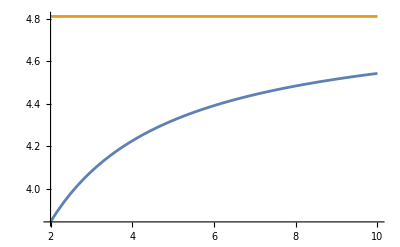

10.1613

```mathematica
f[k_]:=(1+Sin[Pi/(2*(2k+1))])^(2k+1);
Plot[{f[k], Exp[Pi/2]}, {k, 2, 10}]
```

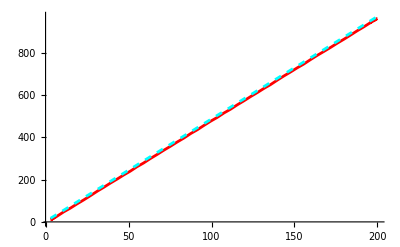

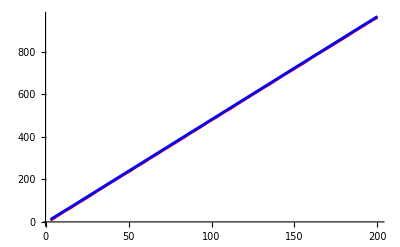

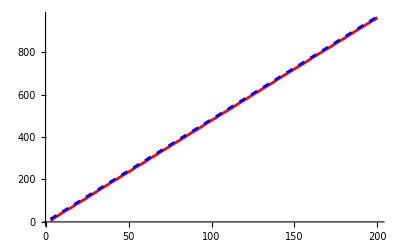

```mathematica
f[k_]:=2*Sin[Pi/(2*(2k+1))]*Sum[(1+Sin[Pi/(2*(2k+1))])^j, {j, 0, 2k-1}]+2*Sum[Sin[(Pi/(2*(2k+1)))*(2k-j)]*(1+Sin[Pi/(2*(2k+1))])^j, {j, 0, 2k-1}];
f1[k_]:=2*Sin[Pi/(2*(2k+1))]*Sum[(1+Sin[Pi/(2*(2k+1))])^j, {j, 0, 2k-1}];
f2[k_]:=2*Sum[Sin[(Pi/(2*(2k+1)))*(j)]*alpha[k]^(2k-j), {j, 0, 2k-1}];
f1apprx[k_]:=2*(Exp[Pi/2]-1);
alpha[k_]:=(1+Sin[Pi/(2*(2k+1))]);
the[k_]:=Pi/(2*(2k+1));
f2apprx[k_]:=1*(Exp[Pi/2]-1)/Sin[Pi/(2*(2k+1))];
f2apprx2[k_]:=2*(1+alpha[k]^(2k+1)*Sin[Pi/(2*(2k+1))]-alpha[k])/(1-alpha[k])^2;
f2apprx3[k_]:=2*Im[(Exp[I*2k*the[k]]*(1-alpha[k]^(2k)Exp[-I*2k*the[k]]))/(1-alpha[k]*Exp[-I*the[k]])];
f2apprx4[k_]:=2*Re[(Sin[2*k*the[k]]-alpha[k]*Sin[(2k+1)*the[k]]+alpha[k]^(2k+1)Sin[the[k]])/(1+alpha[k]^2-2alpha[k]*Cos[the[k]])];
f2apprx5[k_]:=2*Re[(1+alpha[k]^(2k+1)Sin[the[k]]-alpha[k])/(1+alpha[k]^2-2alpha[k]*Cos[the[k]])];
f2apprx6[k_]:=2*Re[(1+alpha[k]^(2k+1)Sin[the[k]]-alpha[k])]*(1/(2 the[k]^2)(*-1/(4*the[k])*));
fx1[k_]:=(1+alpha[k]^2-2alpha[k]*Cos[the[k]]);
fxapprx[k_]:=(1-alpha[k])^2;


(*Plot[{f1[k], f1apprx[k]}, {k, 3, 200}, PlotStyle->{Red, Blue}];*)
Plot[{f2[k], f2apprx[k]}, {k, 3, 200}, PlotStyle->{Red, {Cyan, Dashed}}]
Plot[{f2[k], f2apprx4[k]}, {k, 3, 200}, PlotStyle->{Red, Blue}]
Plot[{f2[k], f2apprx6[k]}, {k, 3, 200}, PlotStyle->{Red, {Blue,Dashed}}]
Plot[{1/fx1[k], 1/fxapprx[k]}, {k, 3, 30}, PlotStyle->{Red, Blue}];
```

```mathematica
fs[x_]:=1+(1+Sin[x])^2-2(1+Sin[x])*Cos[x];
Series[fs[q], {q, 0, 3}]
```

2 q^2+q^3+O[q]^4

```mathematica
c1=2*(Exp[Pi/2]-1);
(1+1/3)*c1//N
2/3*c1*k//N
```

10.1613

5.08064 k

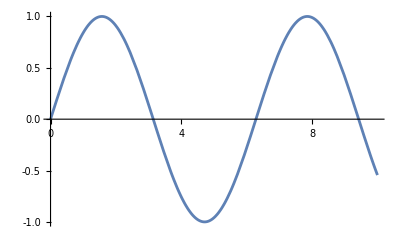

```mathematica
p=Plot[Sin[x],{x,0,10}];

Show[p,Ticks->AbsoluteOptions[p,Ticks][[1,2]]/. {val_,lab_,___}:>{val,lab,{1}}]
```

```mathematica
c0=Exp[Pi/2]-1;
2*c0(1+1/3)//N
4c0/3//N
```

10.1613

5.08064

```mathematica
TrigReduce[Sin[t]^2]
```

1/2 (1-Cos[2 t])

```mathematica
f[th_]:=(1+Exp[I*2*th])/(1-Exp[I*2*th]);
cth[th_]:=1/2*(f[th]+f[-th]);
sth[th_]:=1/(2I)*(f[th]-f[-th]);
(*sth[th]
Cot[th]*)
(*TrigReduce[sth[th]]//FullSimplify*)
Series[sth[θ], {θ, 0, 5}]
Series[Cot[θ], {θ, 0, 5}]
```

1/θ-θ/3-θ^3/45-(2 θ^5)/945+O[θ]^6

1/θ-θ/3-θ^3/45-(2 θ^5)/945+O[θ]^6

```mathematica
f[j_, k_]:=Cos[2j*Pi/(2*(2k+1))];
Table[f[j, 10], {j, 1, 20}]//N
```

{0.988831,0.955573,0.900969,0.826239,0.733052,0.62349,0.5,0.365341,0.222521,0.0747301,-0.0747301,-0.222521,-0.365341,-0.5,-0.62349,-0.733052,-0.826239,-0.900969,-0.955573,-0.988831}

8333.33

6.80175

0.0180607

0.0912423

1000.

2.26725

444.444

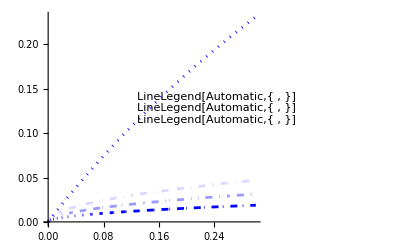

```mathematica
(*slightly different loss function*)
ploss[ki_, kx_, gam_, g_, k_]:=ki/kx*(k+1)*Sin[Pi/(2*(2k+1))]^2+ 4(k)*kx*gam/g^2;
ploss0[ki_, kx_, gam_, g_]:= 1-kx/(ki+kx)*(g^2/((ki+kx)*gam))/((g^2/((ki+kx)*gam))+1);

plossapprx[ki_, kx_, gam_, g_, k_]:= (k)*kx*gam/g^2+Pi^2/(16*k)*ki/kx;
Cex[ki_, kx_, gam_, g_ ]:=(kx*gam/g^2)^-1;
f11[k_]:=(k+1)*Sin[Pi/(2*(2k+1))]^2;
fopt[ki_, kx_, gam_, g_ ]:=Pi/8*Sqrt[ki/kx*g^2/(kx*gam)];

plossOpt[ki_ , kx_ , gam_, g_  ]:=ploss[ki , kx , gam , g , Ceiling[fopt[ki  , kx , gam , g  ]]];


Cex[0.1, 1, 0.003, 5]
fopt[0.1, 1, 0.003, 3]
ploss[0.1, 1, 0.003, 3, fopt[0.1, 1, 0.003, 3]]
ploss0[0.1, 1, 0.003, 3]
Cex[0.1, 3, 0.003, 3]
fopt[0.1, 3, 0.003, 3]
Cex[0.1, 3, 0.003, 2]
Plot[{ploss[0.1, 1, 0.003, 3, k], ploss0[0.1,1, 0.003, 3, k], ploss[0.1, 3, 0.003, 3, k], ploss0[0.1,3, 0.003, 3, k]}, {k, 1, 15}, PlotStyle->{{Red},{Red, Dashed}, {Green},{Green, Dashed}}];
Plot[{ploss[0.1, 1, 0.003, 3, k], plossapprx[0.1,1, 0.003, 3, k]}, {k, 1, 15}, PlotStyle->{{Red, Dashed},{Green, Dashed}}];
(*Plot[{f11[n], Pi^2/(16n)},{n, 1, 12}, PlotStyle->{Red, {Green, Dashed}}]*)
lossplot =Plot[{ plossOpt[x, 1, 0.003, 5], plossOpt[x, 1, 0.003, 3],plossOpt[x, 1, 0.003,2], ploss0[x,1, 0.003, 5],ploss0[x,1, 0.003, 3],ploss0[x,1, 0.003, 2]}, {x, 0, 0.3}, PlotStyle->{{Directive[Blue,Opacity[1]],DotDashed},{Directive[Blue,Opacity[0.4]],DotDashed},{Directive[Blue,Opacity[0.15]],DotDashed},{Directive[Blue,Opacity[1]], Dotted},{Directive[Blue,Opacity[0.4]], Dotted},{Directive[Blue,Opacity[0.15]], Dotted}} ,PlotLegends->Placed[Grid[Partition[LineLegend[Automatic,#]&/@{{" "," "},{" "," "},{" "," "}},1],Spacings->{Automatic,0.15}  (*only vertical tightened*)],{0.80,0.55}]]
```

```mathematica
plossOpt[0.25, 1, 0.003, 5]
```

0.017676

```mathematica
TrigReduce[-2 Sin[τ/2]^2+Cos[τ]]
```

-1+2 Cos[τ]

```mathematica
TrigReduce[Cos[τ]^2]
```

1/2 (1+Cos[2 τ])

```mathematica
TrigReduce[Sin[τ]^2]
```

1/2 (1-Cos[2 τ])

```mathematica
Expand[(a+b+cc)^2]
```

a^2+2 a b+b^2+2 a cc+2 b cc+cc^2

```mathematica
f[th_]:=(Exp[I*th]-I)/(1-Exp[I*th]);
f2[th_]:=(Exp[-I*th]+I)/(1-Exp[-I*th]);
c11[th_]:=1/2*(f[th]+f2[th]);
s11[th_]:=1/(2I)*(f[th]-f2[th]);
c11[11]//N
s11[11]//N
FullSimplify[c11[th1] ]
FullSimplify[s11[th1] ]
```

-1.00222+0. ⅈ

-1.00222+0. ⅈ

1/2 (-1+Cot[th1/2])

1/2 (-1+Cot[th1/2])

```mathematica
TrigToExp[Cos[j*τ]*Sin[j*τ]^2]//Expand
```

1/8 ⅇ^(-ⅈ j τ)+1/8 ⅇ^(ⅈ j τ)-1/8 ⅇ^(-3 ⅈ j τ)-1/8 ⅇ^(3 ⅈ j τ)

```mathematica
TrigReduce[Cos[j*τ]*Sin[jτ]^2]//Expand
```

1/2 Cos[j τ]-1/4 Cos[2 jτ-j τ]-1/4 Cos[2 jτ+j τ]

```mathematica
ⅇ^(2 ⅈ jτ-ⅈ j τ)//FullSimplify
```

ⅇ^(2 ⅈ jτ-ⅈ j τ)

```mathematica
f1[th_]:=1/8*(Exp[I*th]-I)/(1-Exp[I*th]);
f2[th_]:=1/8*(Exp[-I*th]+I)/(1-Exp[-I*th]);
f3[th_]:=1/8*(Exp[I*3*th]+I)/(1-Exp[I*3*th]);
f4[th_]:=1/8*(Exp[-I*3*th]-I)/(1-Exp[-I*3*th]);
ter[th_]:=f1[th]+f2[th]-f3[th]-f4[th];
ter2[τ_]:=1/2 Cos[τ/2] *Cos[τ]/ Sin[(3 τ)/2];
ter[13]//N
ter2[13]//N
```

0.731745+0. ⅈ

0.731745

```mathematica
f[x_]:=(Exp[I*2x]+1)/(1-Exp[I*2x]);
f[ϵ]+f[-ϵ]//Simplify
```

0

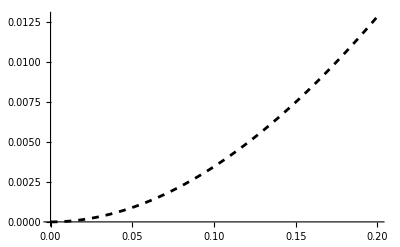

```mathematica
(*Delete later. Checking convexity bounds*)
Plot[{ 1/Sqrt[1+x]-(1-x/2 )}, {x, 0, 0.2}, PlotStyle->{Red, {Black, Dashed}}]
```

```mathematica
AsymptoticEquivalent[1/Sqrt[n!],n->Infinity]
Asymptotic[n!,Sqrt[2 π n] (n/E)^n,{n}]
```

AsymptoticEquivalent::argt: AsymptoticEquivalent called with 2 arguments; 3 or 4 arguments are expected.

AsymptoticEquivalent[1/(√(n!)),n→∞]

Asymptotic::nonopt: Options expected (instead of {n}) beyond position 2 in Asymptotic[n!,ⅇ^-n n^(1/2+n) √(2 π),{n}]. An option must be a rule or a list of rules.

Asymptotic[n!,ⅇ^-n n^(1/2+n) √(2 π),{n}]

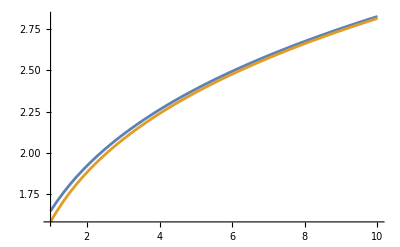

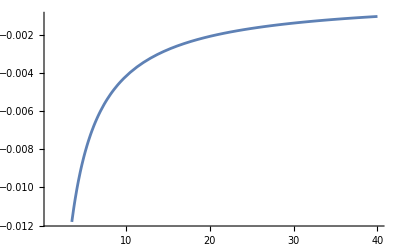

```mathematica
fn1[n_]:=Exp[-n/2] n^(n/2)/Sqrt[n!];
fn1apprx[n_]:=1/((2*Pi)^(1/4)n^(1/4));
Plot[{1/fn1[n],1/ fn1apprx[n]}, {n, 1, 10}]
Plot[{(fn1[n]- fn1apprx[n])/fn1[n]}, {n, 1, 40}]
```

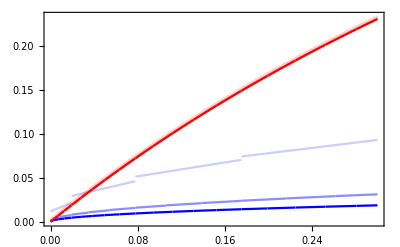

```mathematica
hey1=Plot[{plossOpt[x,1,0.003,5],ploss0[x,1,0.003,5] },{x,0,0.3},PlotStyle->{{Directive[Blue,Opacity[1]] },{Directive[Red,Opacity[1]] } },PlotLegends->Placed[ LineLegend[{" "," ", " ", " ", " ", " "},Spacings->0.01],{0.12,0.9} ],Frame->True];
hey2=Plot[{plossOpt[x,1,0.003,3],ploss0[x,1,0.003,3]  },{x,0,0.3},PlotStyle->{{Directive[Blue,Opacity[0.45]] },{Directive[Red,Opacity[0.45]] }},PlotLegends->Placed[ LineLegend[{" "," ", " ", " ", " ", " "},Spacings->0.01],{0.12,0.7} ],Frame->True];
hey3=Plot[{ plossOpt[x,1,0.003,1],ploss0[x,1,0.003,1]},{x,0,0.3},PlotStyle->{{Directive[Blue,Opacity[0.2]] },{Directive[Red,Opacity[0.2]] }},PlotLegends->Placed[ LineLegend[{" "," ", " ", " ", " ", " "},Spacings->0.01],{0.12,0.5} ], Frame->True];
lossplot =Show[hey3, hey2, hey1]
(*Export["lossplot2.eps",lossplot]*)
```

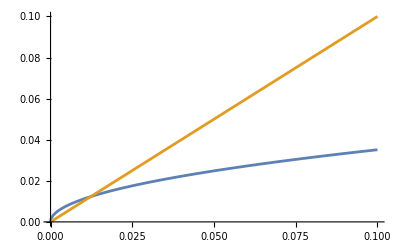

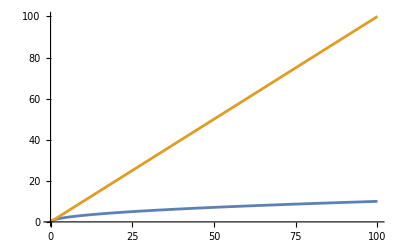

```mathematica
Plot[{Pi/Sqrt[800] Sqrt[x], x}, {x, 0, 0.1}]
Plot[{ Sqrt[x], x}, {x, 0, 100}]
```

```mathematica
16.95 + 24.95+3
```

44.9

```mathematica
(3/44.9)*57.11
```

3.81581

```mathematica
(24.95/44.9)*57.11
```

31.7348

```mathematica
(16.95/44.9)*57.11
```

21.5593

```mathematica
y = ki/kx;
x=Cop^-1;
Series[(1/(x1+1)), {x1, 0, 2}, {y1, 0, 2}]
```

1-x1+x1^2+O[x1]^3